reactions and transitions: (0→s | mu0 s0
i1+s→2 i1 | (i1 mu1 R1 s)/s0
i2+s→2 i2 | (i2 mu2 R2 s)/s0
i12+s→2 i12 | (i12 mu3 R3 s)/s0
i1+i2→i12+i2 | ga1 i1 i2
i1+i2→i1+i12 | ga2 i1 i2
i1+i12→2 i12 | et1 i1 i12
i12+i2→2 i12 | et2 i12 i2
i12+s→i1+i12 | be1 i12 s
i12+s→i12+i2 | be2 i12 s
s→0 | mu0 s
i1→0 | i1 mu1
i2→0 | i2 mu2
i12→0 | i12 mu3)

minimal siph={{{i1,i12},{i2,i12}},{{i1,i2,i12}}}

autocat. sets={{{i1},{i2},{i12}},{{i1,i12},{i1,i2},{i2,i12}}}

Minimal siphons: {T_1→{i1,i12},T_2→{i2,i12}}

IGMS edges: {1->2,2->1}

Cycles found: 1

Cycles: {{1->2,2->1}}

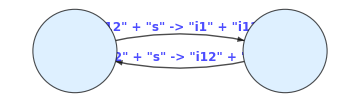

Ko.pdf

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];
<<EpidCRN`;

(*Two-Strain Coinfection Model with Logistic Growth*)
RN={0->"s","s"+"i1"->2*"i1","s"+"i2"->2*"i2","s"+"i12"->2*"i12","i1"+"i2"->"i2"+"i12","i1"+"i2"->"i1"+"i12","i1"+"i12"->2*"i12","i2"+"i12"->2*"i12","s"+"i12"->"i1"+"i12","s"+"i12"->"i2"+"i12","s"->0,"i1"->0,"i2"->0,"i12"->0};
rts={s0 mu0,mu1 s0^(-1)  *R1*s*i1,mu2  s0^(-1)  *R2*s*i2,mu3  s0^(-1)  *R3*s*i12,ga1*i1*i2,ga2*i1*i2,et1*i1*i12,et2*i2*i12,be1*s*i12,be2*s*i12,mu0*s,mu1*i1,mu2*i2,mu3*i12};
Print["reactions and transitions: ",Transpose[{RN,rts}]//MatrixForm]
{spe, al, be, gamma, Rv, RHS, mSi, {defFormula, defTerms, defResult}}=extMat[RN];
Print["minimal siph=",minSiph[spe,RN]]
Print["autocat. sets=",findCores[RN,2]]
{edg,lab,cycles,g}=IGMS[RN,mSi]; 
Export["Ko.pdf",g]
```

```mathematica
{RHS, var, par, cp, mSi, Jx, Jy, E0, K, R0A, infVars,al,be,gam,ng}= bdAn[RN,rts];
Print["siphons are",mSi," source, prod. matr are",al//MatrixForm,be//MatrixForm,"  DFE is",E0," repr. functions=  ",R0A];
F=ng[[2]];V=ng[[3]];per={1,3,2};
Print["F,V,K=",F//MatrixForm,V//MatrixForm,K//MatrixForm,"K permuted",K[[per,per]]//MatrixForm];
```

siphons are{{i1},{i2},{i3}} source, prod. matr are(0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1)(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0)  DFE is{i1→0,i2→mu3/ro23,i3→-mu2/ro23,s→La/mu0,i1→0,i2→0,i3→0,s→La/mu0,i1→(be1 La-mu0 mu1)/(be1 mu1),i2→0,i3→0,s→mu1/be1,i1→mu2/ro12,i2→(-be1 mu1 mu2+be1 La ro12-mu0 mu1 ro12)/(ro12 (be1 mu2+mu0 ro12)),i3→0,s→(La ro12)/(be1 mu2+mu0 ro12),i1→(-mu0 mu3 ro12+be1 La ro23-mu0 mu1 ro23)/(be1 (mu3 ro12+mu1 ro23)),i2→mu3/ro23,i3→(-be1 mu2 mu3 ro12-mu0 mu3 ro12^2-be1 mu1 mu2 ro23+be1 La ro12 ro23-mu0 mu1 ro12 ro23)/(be1 ro23 (mu3 ro12+mu1 ro23)),s→(mu3 ro12+mu1 ro23)/(be1 ro23),i1→0,i2→0,i3→0} repr. functions=  Eigenvalues[0.Inverse[-{}{}]]

Part::partd: Part specification (0.Inverse[-{])⟦{1,3,2},{1,3,2}⟧ is longer than depth of object.

F,V,K=0-{}{}0.Inverse[-{}{}]K permuted(0.Inverse[-{}{}])⟦{1,3,2},{1,3,2}⟧

```mathematica
(*particular cases*)
cLog={be1->0,be2->0,ga1->0,ga2->0,b->r*s*(1-s/s0),mu0->0};
cbg={be1->0,be2->0,ga1->0,ga2->0};
cbe={be1->0,be2->0};cb=b->s0 mu0;cga={ga1->0,ga2->0};
cet={et1->s13 mu1 mu3 (R1-R3)/((s0-s13)mu0 s0),
et2->s23 mu2 mu3 (R2-R3)/((s0-s23)mu0 s0)};
cmu={mu2 ->mu,mu3->mu,mu1 ->mu,mu0->mu};
c3={i12->0};c2={i2->0};c1={i1->0};cb=b->r*s*(1-s/s0);
```

reactions and transitions: (0→s | mu0 s0
i1+s→2 i1 | (i1 mu1 R1 s)/s0
i2+s→2 i2 | (i2 mu2 R2 s)/s0
i12+s→2 i12 | (i12 mu3 R3 s)/s0
i1+i12→2 i12 | et1 i1 i12
i12+i2→2 i12 | et2 i12 i2
s→0 | mu0 s
i1→0 | i1 mu1
i2→0 | i2 mu2
i12→0 | i12 mu3)

eq0{-mu0 s+mu0 s0==0,True,True,True}v0={s}

mSi={{i1},{i2},{i12}}  DFE is{s→s0,i1→0,i12→0,i2→0}

Minimal siphons: {T_1→{i1},T_2→{i2},T_3→{i12}}

IGMS edges: {1->3,2->3}

IGMS is acyclic

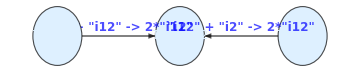

I2c.pdf

```mathematica
(*be=ga=0*)RN={0->"s","s"+"i1"->2*"i1","s"+"i2"->2*"i2","s"+"i12"->2*"i12","i1"+"i12"->2*"i12","i2"+"i12"->2*"i12","s"->0,"i1"->0,"i2"->0,"i12"->0};

rts={s0 mu0,mu1 s0^(-1)  *R1*s*i1,mu2  s0^(-1)  *R2*s*i2,mu3  s0^(-1)  *R3*s*i12,et1*i1*i12,et2*i2*i12,mu0*s,mu1*i1,mu2*i2,mu3*i12};
Print["reactions and transitions: ",Transpose[{RN,rts}]//MatrixForm]
{RHS, var, par, cp, mSi, Jx, Jy, E0, K, R0A, infVars,alp, bet,gam,ng}= bdAn[RN,rts];
Print["mSi=",mSi,"  DFE is",E0];
{edg,lab,cyc,gr}=IGMS[RN, mSi];Export["I2c.pdf",gr]
```

```mathematica
F=ng[[2]];V=ng[[3]];
Print["K=",K//MatrixForm,"F=",F//MatrixForm,"V=",V//MatrixForm];
```

K=((R1 s)/s0 | 0 | 0
0 | (R3 s)/s0 | 0
0 | 0 | (R2 s)/s0)F=((mu1 R1 s)/s0 | 0 | 0
0 | (mu3 R3 s)/s0 | 0
0 | 0 | (mu2 R2 s)/s0)V=(mu1 | 0 | 0
0 | mu3 | 0
0 | 0 | mu2)

```mathematica
{RHS, var, par, cp, mSi, Jx, Jy, E0, K, R0A, infV,gam,Et}=bdCo[RNbg, rtsbg];
Print["The ", Et//Length ," Et elts have  3,3,2 coms "];
Print["Et1= ",Et1=Et[[1]],"Et2= ",
Et2=Et[[2]],"Et3= ",
Et3=Et[[3]]];
eq=Thread[(RHS/.cbg/.c2)==0];
so=Solve[eq,var]//FullSimplify;(*4 solutions*)
Print["the",so//Length,"sols on siphon 2 are",so];
jac=Grad[RHS,var];
```

The 3 Et elts have  3,3,2 coms

Et1= {{i_12→0,i_2→(μ_0 (-1+R_2) s_0)/(μ_2 R_2),s→s_0/R_2,i_1→0},{i_12→(μ_0 (-1+R_3) s_0)/(μ_3 R_3),i_2→0,s→s_0/R_3,i_1→0},{i_12→-(μ_2 (μ_2 μ_3 R_2-μ_2 μ_3 R_3+η_2 μ_0 s_0-η_2 μ_0 R_2 s_0))/(η_2 (μ_2 μ_3 R_2-μ_2 μ_3 R_3+η_2 μ_0 s_0)),i_2→(μ_2 μ_3^2 R_2-μ_2 μ_3^2 R_3+η_2 μ_0 μ_3 s_0-η_2 μ_0 μ_3 R_3 s_0)/(η_2 (μ_2 μ_3 R_2-μ_2 μ_3 R_3+η_2 μ_0 s_0)),s→(η_2 μ_0 s_0^2)/(μ_2 μ_3 R_2-μ_2 μ_3 R_3+η_2 μ_0 s_0),i_1→0}}Et2= {{i_1→(μ_0 (-1+R_1) s_0)/(μ_1 R_1),i_12→0,s→s_0/R_1,i_2→0},{i_1→0,i_12→(μ_0 (-1+R_3) s_0)/(μ_3 R_3),s→s_0/R_3,i_2→0},{i_1→(μ_1 μ_3^2 R_1-μ_1 μ_3^2 R_3+η_1 μ_0 μ_3 s_0-η_1 μ_0 μ_3 R_3 s_0)/(η_1 (μ_1 μ_3 R_1-μ_1 μ_3 R_3+η_1 μ_0 s_0)),i_12→-(μ_1 (μ_1 μ_3 R_1-μ_1 μ_3 R_3+η_1 μ_0 s_0-η_1 μ_0 R_1 s_0))/(η_1 (μ_1 μ_3 R_1-μ_1 μ_3 R_3+η_1 μ_0 s_0)),s→(η_1 μ_0 s_0^2)/(μ_1 μ_3 R_1-μ_1 μ_3 R_3+η_1 μ_0 s_0),i_2→0}}Et3= {{i_1→(μ_0 (-1+R_1) s_0)/(μ_1 R_1),i_2→0,s→s_0/R_1,i_12→0},{i_1→0,i_2→(μ_0 (-1+R_2) s_0)/(μ_2 R_2),s→s_0/R_2,i_12→0}}

Solve::svars: Equations may not give solutions for all "solve" variables.

the4sols on siphon 2 are{{s→s_0,i_1→0,i_12→0},{s→s_0/R_1,i_1→(μ_0 (-1+R_1) s_0)/(μ_1 R_1),i_12→0},{s→s_0/R_3,i_1→0,i_12→(μ_0 (-1+R_3) s_0)/(μ_3 R_3)},{s→(η_1 μ_0 s_0^2)/(μ_1 μ_3 (R_1-R_3)+η_1 μ_0 s_0),i_1→(μ_3 (μ_1 μ_3 (R_1-R_3)-η_1 μ_0 (-1+R_3) s_0))/(η_1 (μ_1 μ_3 (R_1-R_3)+η_1 μ_0 s_0)),i_12→(μ_1 (μ_1 μ_3 (-R_1+R_3)+η_1 μ_0 (-1+R_1) s_0))/(η_1 (μ_1 μ_3 (R_1-R_3)+η_1 μ_0 s_0))}}

```mathematica
(*all fps*)
eq=Thread[RHS==0];so=Solve[eq,var];(*7 solutions*)
Print[so//Length," sols"]
so//FullSimplify
cD=so[[1]];cE1=so[[2]];cE2=so[[3]];cE3=so[[5]];cEE=so[[4]];c13=so[[6]];
Print["s13= ",s13=s/.c13//FullSimplify]
i131=i1/.c13; i131-mu3(1-R3 s13/s0) /et1//FullSimplify
i133=i12/.c13//FullSimplify;
i133-(R1 s13/s0 -1)mu1/et1//FullSimplify
c23=so[[7]];
con=Join[cp,Thread[Drop[var/.cE1,{3,4}]>0]];
jEE=jac/.cEE//FullSimplify;
(*Print[" At cE1, chp of jac, ch1, factorizes as"]
ch1=Numerator[Together[CharacteristicPolynomial[jEE,u]]]//Factor*)
EE=var/.cEE;
ine=Join[Thread[EE>0],cp,{et1 mu2>et2 mu1,R2<R1<R2 et1 mu2/et2 mu1}]
ret=Reduce[ine/.cmu];re=FullSimplify[ret,cp]
(*{lSta,qSta,hDeg,ll,ql}=sta[ch1,par];
ll//Length
ql//Length
hDeg*)

(*con=Join[cp,Thread[Drop[var/.c13,3]>0]];
Print["E13 exists if"]
re11=reCL[Reduce[con]//Factor]*)
```

7 sols

{{s→s_0,i_1→0,i_2→0,i_12→0},{s→s_0/R_1,i_1→(μ_0 (-1+R_1) s_0)/(μ_1 R_1),i_2→0,i_12→0},{s→s_0/R_2,i_1→0,i_2→(μ_0 (-1+R_2) s_0)/(μ_2 R_2),i_12→0},{s→((η_2 μ_1-η_1 μ_2) s_0)/(η_2 μ_1 R_1-η_1 μ_2 R_2),i_1→(μ_2 (-η_2 μ_1+η_1 μ_2) μ_3 (R_2-R_3)+η_2 μ_0 (η_2 μ_1 (-1+R_1)-η_1 μ_2 (-1+R_2)) s_0)/((η_2 μ_1-η_1 μ_2) (η_2 μ_1 R_1-η_1 μ_2 R_2)),i_2→(μ_1 (η_2 μ_1-η_1 μ_2) μ_3 (R_1-R_3)+η_1 μ_0 (η_2 (μ_1-μ_1 R_1)+η_1 μ_2 (-1+R_2)) s_0)/((η_2 μ_1-η_1 μ_2) (η_2 μ_1 R_1-η_1 μ_2 R_2)),i_12→(μ_1 μ_2 (-R_1+R_2))/(η_2 μ_1 R_1-η_1 μ_2 R_2)},{s→s_0/R_3,i_1→0,i_2→0,i_12→(μ_0 (-1+R_3) s_0)/(μ_3 R_3)},{s→(η_1 μ_0 s_0^2)/(μ_1 μ_3 (R_1-R_3)+η_1 μ_0 s_0),i_1→(μ_3 (μ_1 μ_3 (R_1-R_3)-η_1 μ_0 (-1+R_3) s_0))/(η_1 (μ_1 μ_3 (R_1-R_3)+η_1 μ_0 s_0)),i_2→0,i_12→(μ_1 (μ_1 μ_3 (-R_1+R_3)+η_1 μ_0 (-1+R_1) s_0))/(η_1 (μ_1 μ_3 (R_1-R_3)+η_1 μ_0 s_0))},{s→(η_2 μ_0 s_0^2)/(μ_2 μ_3 (R_2-R_3)+η_2 μ_0 s_0),i_1→0,i_2→(μ_3 (μ_2 μ_3 (R_2-R_3)-η_2 μ_0 (-1+R_3) s_0))/(η_2 (μ_2 μ_3 (R_2-R_3)+η_2 μ_0 s_0)),i_12→(μ_2 (μ_2 μ_3 (-R_2+R_3)+η_2 μ_0 (-1+R_2) s_0))/(η_2 (μ_2 μ_3 (R_2-R_3)+η_2 μ_0 s_0))}}

s13= (η_1 μ_0 s_0^2)/(μ_1 μ_3 (R_1-R_3)+η_1 μ_0 s_0)

0

0

{((η_2 μ_1-η_1 μ_2) s_0)/(η_2 μ_1 R_1-η_1 μ_2 R_2)>0,(-η_2 μ_1 μ_2 μ_3 R_2+η_1 μ_2^2 μ_3 R_2+η_2 μ_1 μ_2 μ_3 R_3-η_1 μ_2^2 μ_3 R_3-η_2^2 μ_0 μ_1 s_0+η_1 η_2 μ_0 μ_2 s_0+η_2^2 μ_0 μ_1 R_1 s_0-η_1 η_2 μ_0 μ_2 R_2 s_0)/((η_2 μ_1-η_1 μ_2) (η_2 μ_1 R_1-η_1 μ_2 R_2))>0,(η_2 μ_1^2 μ_3 R_1-η_1 μ_1 μ_2 μ_3 R_1-η_2 μ_1^2 μ_3 R_3+η_1 μ_1 μ_2 μ_3 R_3+η_1 η_2 μ_0 μ_1 s_0-η_1^2 μ_0 μ_2 s_0-η_1 η_2 μ_0 μ_1 R_1 s_0+η_1^2 μ_0 μ_2 R_2 s_0)/((η_2 μ_1-η_1 μ_2) (η_2 μ_1 R_1-η_1 μ_2 R_2))>0,-(μ_1 μ_2 (R_1-R_2))/(η_2 μ_1 R_1-η_1 μ_2 R_2)>0,η_1>0,η_2>0,μ_0>0,μ_1>0,μ_2>0,μ_3>0,R_1>0,R_2>0,R_3>0,s_0>0,η_1 μ_2>η_2 μ_1,R_2<R_1<(η_1 μ_1 μ_2 R_2)/η_2}

R_2>1&&R_1>R_2&&η_1>(η_2 (-1+R_1))/(-1+R_2)&&R_3<(-η_2 R_1+η_1 R_2)/(η_1-η_2)&&μ>√((η_2 R_1)/(η_1 R_2))&&((η_1-η_2) μ (R_1-R_3))/(η_1 (η_2-η_2 R_1+η_1 (-1+R_2)))<s_0<-((η_1-η_2) μ (R_2-R_3))/(η_2 (η_1+η_2 (-1+R_1)-η_1 R_2))

```mathematica
re
```

R_1>1&&R_3<(η_2 μ_1 R_1-η_1 μ_2 R_2)/(η_2 μ_1-η_1 μ_2)&&(μ_1 (-η_2 μ_1+η_1 μ_2) μ_3 (R_1-R_3))/(η_1 (η_2 (μ_1-μ_1 R_1)+η_1 μ_2 (-1+R_2)) s_0)<μ_0<(μ_2 (η_2 μ_1-η_1 μ_2) μ_3 (R_2-R_3))/(η_2 (η_2 μ_1 (-1+R_1)-η_1 μ_2 (-1+R_2)) s_0)&&((R_2>1&&(μ_1≥1||R_2≤R_1/(-μ_1^2 (-1+R_1)+R_1))&&(μ_1<1||R_2<R_1)&&η_1>(η_2 μ_1 (-1+R_1))/(μ_2 (-1+R_2)))||(η_1 μ_1 μ_2 R_2>η_2 R_1&&R_1/(-μ_1^2 (-1+R_1)+R_1)<R_2<R_1&&μ_1<1))

```mathematica
(*Stab E1*)
j1=jac/.cE1//FullSimplify;j1//MatrixForm
Print[" At cE1, chp of jac, ch1, factorizes as"]
ch1=Numerator[Together[CharacteristicPolynomial[j1,u]]]//Factor
{lSta,qSta,hDeg,ll,ql}=sta[ch1,par];
```

```mathematica
lSta
qSta
Print["E1 stable if R1(s13) >1"]
re=reCL[Reduce[Join[cp,lSta,qSta]]//FullSimplify]//FullSimplify
cpL=And@@Drop[cp,-1]&&R1>1;
re1=FullSimplify[re,cpL]
```

{μ_2 R_1-μ_2 R_2>0,μ_1 μ_3 R_1-μ_1 μ_3 R_3+μ_0 s_0 η_1-μ_0 R_1 s_0 η_1>0}

{μ_0 R_1>0,-μ_0 μ_1+μ_0 μ_1 R_1>0}

E1 stable if R1(s13) >1

(R_1>R_3&&R_3>1&&μ_0<(μ_1 μ_3 (R_1-R_3))/((-1+R_1) s_0 η_1)&&R_2<R_1)||(R_1>1&&R_1>R_2&&μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_1) s_0 η_1<0&&R_3≤1)

μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_1) s_0 η_1<0&&R_1>R_2&&(R_1>R_3||R_3≤1)

```mathematica
(*Stab E3*)j3=jac/.cE3//FullSimplify;j3//MatrixForm
Print[" At cE3, chp of jac, ch3, factorizes as"]
ch3=Numerator[Together[CharacteristicPolynomial[j3,u]]]//Factor
{lSta,qSta,hDeg,ll,ql}=sta[ch3,par];
ll//Length
ql//Length
hDeg

ret=Reduce[Join[cp,lSta,qSta,{R3>1(*,R1>R2*)}]]//FullSimplify;
cond=And@@cp&&R3>1
Print["E3 stable if R1(s11) <1"]
re3=FullSimplify[ret,cond]
re3//Length
re31=re3[[1]]
re31//Length
re32=re3[[2]];re=BooleanMinimize[LogicalExpand[re3]]//FullSimplify
FullSimplify[re3,cond]
FullSimplify[re,cond]
lo=LogicalExpand[re]
Resolve[lo,Reals]
```

(-μ_0 R_3 | -(μ_1 R_1)/R_3 | -(μ_2 R_2)/R_3 | -μ_3
0 | (μ_1 μ_3 (R_1-R_3)-μ_0 (-1+R_3) s_0 η_1)/(μ_3 R_3) | 0 | 0
0 | 0 | (μ_2 μ_3 (R_2-R_3)-μ_0 (-1+R_3) s_0 η_2)/(μ_3 R_3) | 0
μ_0 (-1+R_3) | (μ_0 (-1+R_3) s_0 η_1)/(μ_3 R_3) | (μ_0 (-1+R_3) s_0 η_2)/(μ_3 R_3) | 0)

At cE3, chp of jac, ch3, factorizes as

(-μ_0 μ_3+μ_0 μ_3 R_3+μ_0 R_3 u+u^2) (-μ_1 μ_3 R_1+μ_1 μ_3 R_3+μ_3 R_3 u-μ_0 s_0 η_1+μ_0 R_3 s_0 η_1) (-μ_2 μ_3 R_2+μ_2 μ_3 R_3+μ_3 R_3 u-μ_0 s_0 η_2+μ_0 R_3 s_0 η_2)

2

1

{}

μ_0>0&&μ_1>0&&μ_2>0&&μ_3>0&&R_1>0&&R_2>0&&R_3>0&&s_0>0&&η_1>0&&η_2>0&&R_3>1

E3 stable if R1(s11) <1

(R_1≤R_3||μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0)&&(R_2≤1||R_2≤R_3||μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0)

2

R_1≤R_3||μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0

2

(R_1≤R_3||μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0)&&(R_2≤1||R_2≤R_3||μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0)

(R_1≤R_3||μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0)&&(R_2≤1||R_2≤R_3||μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0)

(R_1≤R_3||μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0)&&(R_2≤1||R_2≤R_3||μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0)

(μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0&&μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0)||(μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0&&R_2≤1)||(μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0&&R_2≤R_3)||(μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0&&R_1≤R_3)||(R_1≤R_3&&R_2≤1)||(R_1≤R_3&&R_2≤R_3)

(μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0&&μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0)||(μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0&&R_2≤1)||(μ_1 μ_3 (-R_1+R_3)+μ_0 (-1+R_3) s_0 η_1>0&&R_2≤R_3)||(μ_2 μ_3 (-R_2+R_3)+μ_0 (-1+R_3) s_0 η_2>0&&R_1≤R_3)||(R_1≤R_3&&R_2≤1)||(R_1≤R_3&&R_2≤R_3)

```mathematica
(*Stab E13*)
j13=jac/.c13//FullSimplify;
Print[" At cE13, chp of jac factorizes as"]
ch13=Numerator[Together[CharacteristicPolynomial[j13,u]]]//Factor
ch13//Length
co2=CoefficientList[ch13[[2]],u]//FullSimplify
```

At cE13, chp of jac factorizes as

(μ_1^4 μ_3^4 R_1^3-3 μ_1^4 μ_3^4 R_1^2 R_3+3 μ_1^4 μ_3^4 R_1 R_3^2-μ_1^4 μ_3^4 R_3^3-μ_1^3 μ_3^3 R_1^3 u^2+3 μ_1^3 μ_3^3 R_1^2 R_3 u^2-3 μ_1^3 μ_3^3 R_1 R_3^2 u^2+μ_1^3 μ_3^3 R_3^3 u^2+3 μ_0 μ_1^3 μ_3^3 R_1^2 s_0 η_1-μ_0 μ_1^3 μ_3^3 R_1^3 s_0 η_1-6 μ_0 μ_1^3 μ_3^3 R_1 R_3 s_0 η_1+μ_0 μ_1^3 μ_3^3 R_1^2 R_3 s_0 η_1+3 μ_0 μ_1^3 μ_3^3 R_3^2 s_0 η_1+μ_0 μ_1^3 μ_3^3 R_1 R_3^2 s_0 η_1-μ_0 μ_1^3 μ_3^3 R_3^3 s_0 η_1+μ_1^3 μ_3^3 R_1^2 s_0 u η_1-μ_0 μ_1^3 μ_3^2 R_1^3 s_0 u η_1-2 μ_1^3 μ_3^3 R_1 R_3 s_0 u η_1+μ_0 μ_1^3 μ_3^2 R_1^2 R_3 s_0 u η_1+μ_1^3 μ_3^3 R_3^2 s_0 u η_1+μ_0 μ_1^2 μ_3^3 R_1 R_3^2 s_0 u η_1-μ_0 μ_1^2 μ_3^3 R_3^3 s_0 u η_1-3 μ_0 μ_1^2 μ_3^2 R_1^2 s_0 u^2 η_1+6 μ_0 μ_1^2 μ_3^2 R_1 R_3 s_0 u^2 η_1-3 μ_0 μ_1^2 μ_3^2 R_3^2 s_0 u^2 η_1-μ_1^2 μ_3^2 R_1^2 s_0 u^3 η_1+2 μ_1^2 μ_3^2 R_1 R_3 s_0 u^3 η_1-μ_1^2 μ_3^2 R_3^2 s_0 u^3 η_1+3 μ_0^2 μ_1^2 μ_3^2 R_1 s_0^2 η_1^2-2 μ_0^2 μ_1^2 μ_3^2 R_1^2 s_0^2 η_1^2-3 μ_0^2 μ_1^2 μ_3^2 R_3 s_0^2 η_1^2+μ_0^2 μ_1^2 μ_3^2 R_1^2 R_3 s_0^2 η_1^2+2 μ_0^2 μ_1^2 μ_3^2 R_3^2 s_0^2 η_1^2-μ_0^2 μ_1^2 μ_3^2 R_1 R_3^2 s_0^2 η_1^2+2 μ_0 μ_1^2 μ_3^2 R_1 s_0^2 u η_1^2-μ_0^2 μ_1^2 μ_3 R_1^2 s_0^2 u η_1^2-μ_0 μ_1^2 μ_3^2 R_1^2 s_0^2 u η_1^2-2 μ_0 μ_1^2 μ_3^2 R_3 s_0^2 u η_1^2+μ_0^2 μ_1^2 μ_3 R_1^2 R_3 s_0^2 u η_1^2+μ_0^2 μ_1 μ_3^2 R_3^2 s_0^2 u η_1^2+μ_0 μ_1^2 μ_3^2 R_3^2 s_0^2 u η_1^2-μ_0^2 μ_1 μ_3^2 R_1 R_3^2 s_0^2 u η_1^2-3 μ_0^2 μ_1 μ_3 R_1 s_0^2 u^2 η_1^2+3 μ_0^2 μ_1 μ_3 R_3 s_0^2 u^2 η_1^2-2 μ_0 μ_1 μ_3 R_1 s_0^2 u^3 η_1^2+2 μ_0 μ_1 μ_3 R_3 s_0^2 u^3 η_1^2+μ_0^3 μ_1 μ_3 s_0^3 η_1^3-μ_0^3 μ_1 μ_3 R_1 s_0^3 η_1^3-μ_0^3 μ_1 μ_3 R_3 s_0^3 η_1^3+μ_0^3 μ_1 μ_3 R_1 R_3 s_0^3 η_1^3+μ_0^2 μ_1 μ_3 s_0^3 u η_1^3-μ_0^2 μ_1 μ_3 R_1 s_0^3 u η_1^3-μ_0^2 μ_1 μ_3 R_3 s_0^3 u η_1^3+μ_0^2 μ_1 μ_3 R_1 R_3 s_0^3 u η_1^3-μ_0^3 s_0^3 u^2 η_1^3-μ_0^2 s_0^3 u^3 η_1^3) (-μ_1 μ_2 μ_3 R_1 η_1+μ_1 μ_2 μ_3 R_3 η_1-μ_1 μ_3 R_1 u η_1+μ_1 μ_3 R_3 u η_1-μ_0 μ_2 s_0 η_1^2+μ_0 μ_2 R_2 s_0 η_1^2-μ_0 s_0 u η_1^2+μ_1^2 μ_3 R_1 η_2-μ_1^2 μ_3 R_3 η_2+μ_0 μ_1 s_0 η_1 η_2-μ_0 μ_1 R_1 s_0 η_1 η_2)

2

{μ_0 μ_2 (-1+R_2) s_0 η_1^2+μ_1^2 μ_3 (R_1-R_3) η_2+μ_1 η_1 (μ_2 μ_3 (-R_1+R_3)-μ_0 (-1+R_1) s_0 η_2),-η_1 (μ_1 μ_3 (R_1-R_3)+μ_0 s_0 η_1)}

```mathematica
v23=Drop[var/.c23//FullSimplify,{2}];
(*Print["E23 exists if"]*)
re2=reCL[Factor/@Reduce[Join[cp,Thread[v23>0]]]];
Print["EE exists if"]
reE=reCL[Factor/@Reduce[Join[cp,Thread[(var/.cEE)>0],{R1>R2}]]]
reE[[2,1]]
```

EE exists if

R_2>1&&R_1>R_2&&0<μ_1<(μ_2 (-1+R_2) η_1)/((-1+R_1) η_2)&&0<R_3<(μ_2 R_2 η_1-μ_1 R_1 η_2)/(μ_2 η_1-μ_1 η_2)&&(μ_1 μ_3 (R_1-R_3) (-μ_2 η_1+μ_1 η_2))/(s_0 η_1 (μ_2 η_1-μ_2 R_2 η_1-μ_1 η_2+μ_1 R_1 η_2))<μ_0<(μ_2 μ_3 (R_2-R_3) (μ_2 η_1-μ_1 η_2))/(s_0 η_2 (-μ_2 η_1+μ_2 R_2 η_1+μ_1 η_2-μ_1 R_1 η_2))

```mathematica
(*Format[mu]:=μ;Format[xi]:=ξ;
Format[ga]:=ga;Format[ga1]:=Subscript[γ,1];Format[ga2]:=Subscript[γ,2];
Format[be1]:=Subscript[β,1];Format[be2]:=Subscript[β,2];
Format[mu1]:=Subscript[μ,1];Format[mu2]:=Subscript[μ,2];Format[mu3]:=Subscript[μ,3];Format[mu0]:=Subscript[μ,0];
Format[R1]:=Subscript[R,1];Format[R2]:=Subscript[R,2];Format[R3]:=Subscript[R,3];
Format[et1]:=Subscript[η,1];Format[et2]:=Subscript[η,2];
Format[ga1]:=Subscript[γ,1];Format[ga2]:=Subscript[γ,2];Format[s0]:=Subscript[s,0];
Format[th]:=θ;
Format[La]:=Λ;
Format[i1]:=Subscript[i,1];Format[i2]:=Subscript[i,2];
Format[i12]:=Subscript[i,12];*)
```

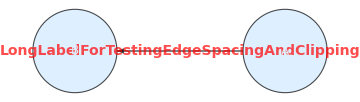

```mathematica
Graph[{1,2},{1->2},DirectedEdges->True,EdgeLabels->{1->2->Placed[Style["LongLabelForTestingEdgeSpacingAndClipping",14,Red,Bold],Center]},VertexLabels->{1->Placed["A",Center],2->Placed["B",Center]},VertexSize->.4,VertexStyle->LightBlue,EdgeStyle->Black,VertexLabelStyle->Directive[FontSize->12],ImageSize->Medium]
```